```mathematica
(*Einstein oscillator 4.685Angstrom*)
cPotentialmeV[x_]:=5991.975480782819*x^2
zrPotentialmeV[x_]:=8248.724499239166*x^2
m={12.0107,91.224,1};
kB=8.6173324*10^-3;
```

```mathematica
(*Define Einstein oscillator frequencies from the harmonic fit prefactors*)(* A*x*x=0.5*m*omega*omega*x*x, so... *)
cOmeg0=Sqrt[2*cPotentialmeV[1]/m[[1]]]
zOmega0=Sqrt[2*zrPotentialmeV[1]/m[[2]]]
```

31.5875

13.4479

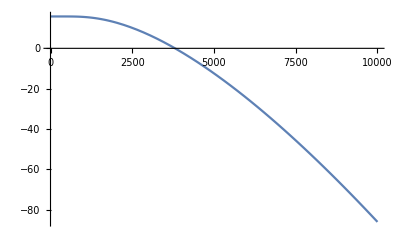

-86.0015

```mathematica
harmonic=Table[0.5+i,{i,0,100}];
energy=cOmeg0*harmonic;
Z[T_]:=Total[Exp[-energy/(kB*T)]]
prefactor[T_]:=Exp[-energy/(kB*T)]
probability[T_]:=(1/Z[T])*prefactor[T]
Z[4000];
probability[4000];
ListPlot[probability[1000],Joined->True];
HelmholtzFree[T_]:=-kB*T*Log[Z[T]]
Plot[HelmholtzFree[T],{T,1,10000}]
HelmholtzFree[10000]
```